# ScalarQED Higgsed

```mathematica
NotebookDirectory[]
```

/home/raj/C_SM/ToySMat1Loop/

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
$model="ScalarQEDHiggsed";
```

```mathematica
<<GenAmp`
```

Patched 2 FeynArts models.

## Setup

```mathematica
$gaugerules=Join[M$IntParams,{FAGaugeXi[S[1]]:> 1}];
```

```mathematica
$ampconfigFCFAConvert={ChangeDimension->D,Contract->False,DropSumOver->False,FCFADiracChainJoin->True,FeynAmpDenominatorCombine->True,
FinalSubstitutions->{},InitialSubstitutions->{},List->False,LoopMomenta->{l},LorentzIndexNames->{},Prefactor->1,SMP->False,SUNFIndexNames->{},
SUNIndexNames->{},TransversePolarizationVectors->{},UndoChiralSplittings->False};
```

## Tadpole (1->0)

## One Loop H->0

loading generic model file /home/raj/C_SM/ToySMat1Loop/models/ScalarQEDHiggsed/ScalarQEDHiggsed.gen

> $GenericMixing is OFF

generic model {./models/ScalarQEDHiggsed/ScalarQEDHiggsed} initialized

loading classes model file /home/raj/C_SM/ToySMat1Loop/models/ScalarQEDHiggsed/ScalarQEDHiggsed.mod

> 5 particles (incl. antiparticles) in 4 classes

> $CounterTerms are ON

> 10 vertices

> 15 counterterms of order 1

classes model {./models/ScalarQEDHiggsed/ScalarQEDHiggsed} initialized

inserting at level(s) {Particles}

> Top. 1: 4 Particles insertions

in total: 4 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ab/0/bb.m, 0 diagrams

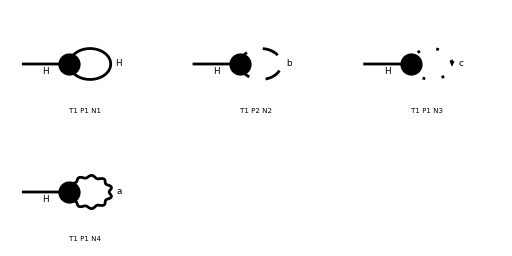

> Top. 1 ab/0/0.m, 0 diagrams

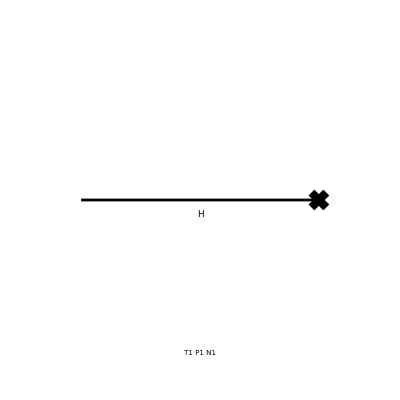

```mathematica
D1LH=diag[1,{S[1]},{}];
```

```mathematica
Amp1LH=D1LH//amp1L[{p1},{}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 4 Particles amplitudes

in total: 4 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

Part::partw: Part 2 of {} does not exist.

{-(ⅈ e^2 vev g^Lor1Lor2 (g^Lor1Lor2/(l^2-e^2 vev^2)-(l^Lor1 l^Lor2 (1-ξ_(V(1))))/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))))))/(16 π^4)-(ⅈ g4 vev)/(64 π^4 (l^2-e^2 vev^2 ξ_(V(1))))+(ⅈ e^2 vev ξ_(V(1)))/(16 π^4 (l^2-e^2 vev^2 ξ_(V(1))))-(3 ⅈ g4 vev)/(64 π^4 (l^2-(g4 vev^2)/2)),-1/4 g4 vev^3 √ZH (Zv-1) Zv (Zv+1)}

```mathematica
Amp1LHDiv=Amp1LH//amp1LSimplify[{Zv:> 1+Nd dv,ZH:> 1+Nd dH},{SMP["Delta"],dv,dH}]
```

-1/2 dv g4 vev^3+(3 Δ e^4 vev^3)/(8 π^2)+(Δ e^2 g4 vev^3 ξ_(V(1)))/(32 π^2)+(3 Δ g4^2 vev^3)/(64 π^2)

```mathematica
dsol[1]=Solve[SelectFree2[Amp1LHDiv,p1]==0,dv]//Flatten//Simplify
dSave[dsol[1]];
```

{dv→(Δ (3 (8 e^4+g4^2)+2 e^2 g4 ξ_(V(1))))/(32 π^2 g4)}

## One Loop (1->1)

## One Loop S->S

inserting at level(s) {Particles}

> Top. 1: 3 Particles insertions

> Top. 2: 5 Particles insertions

in total: 8 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

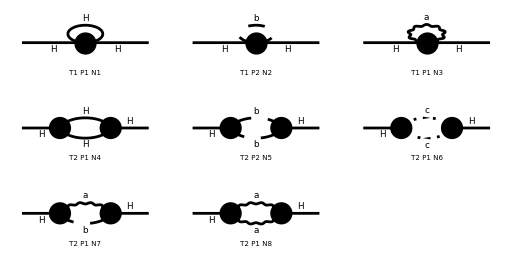

> Top. 1 ac/bc/0.m, 0 diagrams

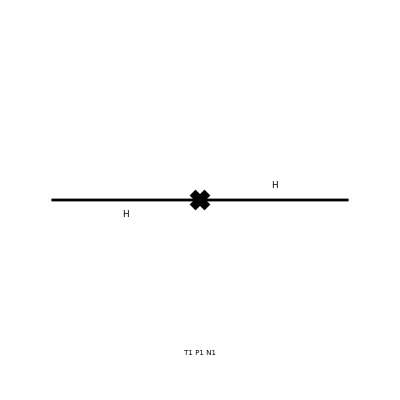

```mathematica
D1LHH=diag[1,{S[1]},{S[1]}];
```

```mathematica
Amp1LHH=D1LHH//amp1L[{p1},{p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 5 Particles amplitudes

in total: 8 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-1/(16 π^4)ⅈ (-e l^Lor1-e p1^Lor1) (e l^Lor2+e p1^Lor2) (g^Lor1Lor2/((l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l-p1)^Lor1 (p1-l)^Lor2)/((l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1)))))-(ⅈ g4^2 vev^2)/(128 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2 ξ_(V(1))))-1/(8 π^4)ⅈ e^4 vev^2 g^Lor1Lor3 g^Lor2Lor4 (-(l^Lor1 l^Lor2 (1-ξ_(V(1))) g^Lor3Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2))+((1-ξ_(V(1))) g^Lor1Lor2 (l-p1)^Lor3 (p1-l)^Lor4)/((l^2-e^2 vev^2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+(g^Lor1Lor2 g^Lor3Lor4)/((l^2-e^2 vev^2).((l-p1)^2-e^2 vev^2))+-(l^Lor1 l^Lor2 (1-ξ_(V(1)))^2 (l-p1)^Lor3 (p1-l)^Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1)))))+(ⅈ e^4 vev^2 ξ_(V(1))^2)/(16 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2 ξ_(V(1))))-(9 ⅈ g4^2 vev^2)/(128 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-(g4 vev^2)/2))-(ⅈ e^2 g^Lor1Lor2 (g^Lor1Lor2/(l^2-e^2 vev^2)-(l^Lor1 l^Lor2 (1-ξ_(V(1))))/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))))))/(16 π^4)-(ⅈ g4)/(64 π^4 (l^2-e^2 vev^2 ξ_(V(1))))-(3 ⅈ g4)/(64 π^4 (l^2-(g4 vev^2)/2)),-ⅈ (ⅈ p1^2 (ZH-1)-1/4 ⅈ g4 vev^2 (2 ZH ZmH^2 Zv^2+ZH Zv^2-ZH-2))}

```mathematica
Amp1LHHDiv=Amp1LHH//amp1LSimplify[{ZH:> 1+Nd dH,ZmH:> 1+Nd dmH,Zv:> 1+Nd dv},{SMP["Delta"],dH, dmH,dv}]
```

-1/2 dH g4 vev^2+dH p1^2-dmH g4 vev^2-3/2 dv g4 vev^2+(9 Δ e^4 vev^2)/(8 π^2)+(Δ e^2 g4 vev^2 ξ_(V(1)))/(32 π^2)-(3 Δ e^2 p1^2)/(8 π^2)+(Δ e^2 p1^2 ξ_(V(1)))/(8 π^2)+(13 Δ g4^2 vev^2)/(64 π^2)

```mathematica
dsol[2]=Solve[SelectNotFree2[Amp1LHHDiv/.dSub[dH],p1]==0,dH]//Flatten//Simplify
dSave[dsol[2]];
```

{dH→-(Δ e^2 (ξ_(V(1))-3))/(8 π^2)}

```mathematica
dsol[3]=Solve[SelectFree2[Amp1LHHDiv/.dSub[dmH],p1]==0,dmH]//Flatten//Simplify
dSave[dsol[3]];
```

{dmH→(Δ (g4-3 e^2))/(16 π^2)}

## One Loop A->A

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 2 Particles insertions

in total: 4 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

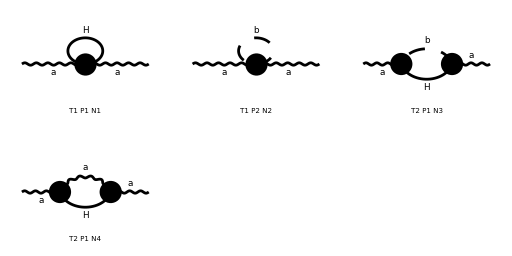

> Top. 1 ac/bc/0.m, 0 diagrams

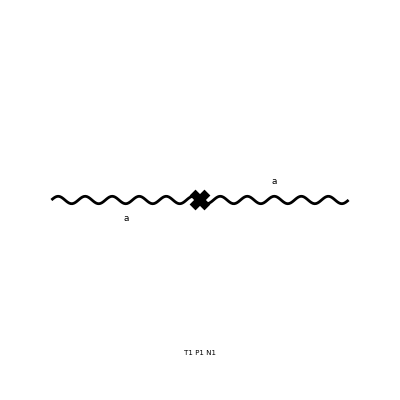

```mathematica
D1LAA=diag[1,{V[1]},{V[1]}];
```

```mathematica
Amp1LAA=D1LAA//amp1L[{p1},{p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 2 Particles amplitudes

in total: 4 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{(ⅈ (e (l-p1)^Lor1+e l^Lor1) (e (p1-l)^Lor2-e l^Lor2))/(16 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+1/(4 π^4)ⅈ e^4 vev^2 g^Lor1Lor3 g^Lor2Lor4 (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1)))))+(ⅈ e^2 g^Lor1Lor2)/(16 π^4 (l^2-(g4 vev^2)/2))+(ⅈ e^2 g^Lor1Lor2)/(16 π^4 (l^2-e^2 vev^2 ξ_(V(1)))),-ⅈ (ⅈ e^2 vev^2 g^Lor1Lor2 (ZA ZmA^2 Zv^2-1)-ⅈ p1^2 (ZA-1) g^Lor1Lor2+(ⅈ p1^Lor1 p1^Lor2 (-ξ_(V(1))+ZA ξ_(V(1))-ZA+1))/(ξ_(V(1))))}

```mathematica
Amp1LAADiv=Amp1LAA//amp1LSimplify[{ZA:> 1+Nd dA,ZmA:> 1+Nd dmA,Zv:> 1+Nd dv},{SMP["Delta"],dA,dmA,dv}]
```

dA e^2 vev^2 g^Lor1Lor2-dA p1^2 g^Lor1Lor2-(dA p1^Lor1 p1^Lor2)/(ξ_(V(1)))+dA p1^Lor1 p1^Lor2+2 dmA e^2 vev^2 g^Lor1Lor2+2 dv e^2 vev^2 g^Lor1Lor2-(Δ e^4 vev^2 ξ_(V(1)) g^Lor1Lor2)/(8 π^2)-(3 Δ e^4 vev^2 g^Lor1Lor2)/(8 π^2)-(Δ e^2 p1^2 g^Lor1Lor2)/(24 π^2)+(Δ e^2 p1^Lor1 p1^Lor2)/(24 π^2)

```mathematica
List@@Amp1LAADiv
```

{dA e^2 vev^2 g^Lor1Lor2,2 dmA e^2 vev^2 g^Lor1Lor2,2 dv e^2 vev^2 g^Lor1Lor2,dA p1^Lor1 p1^Lor2,-(dA p1^Lor1 p1^Lor2)/(ξ_(V(1))),-dA p1^2 g^Lor1Lor2,-(3 Δ e^4 vev^2 g^Lor1Lor2)/(8 π^2),-(Δ e^4 vev^2 ξ_(V(1)) g^Lor1Lor2)/(8 π^2),(Δ e^2 p1^Lor1 p1^Lor2)/(24 π^2),-(Δ e^2 p1^2 g^Lor1Lor2)/(24 π^2)}

```mathematica
Amp1LAADiv=Delete[Amp1LAADiv,{{4},{5},{9}}]
```

dA e^2 vev^2 g^Lor1Lor2-dA p1^2 g^Lor1Lor2+2 dmA e^2 vev^2 g^Lor1Lor2+2 dv e^2 vev^2 g^Lor1Lor2-(Δ e^4 vev^2 ξ_(V(1)) g^Lor1Lor2)/(8 π^2)-(3 Δ e^4 vev^2 g^Lor1Lor2)/(8 π^2)-(Δ e^2 p1^2 g^Lor1Lor2)/(24 π^2)

```mathematica
dsol[4]=Solve[SelectNotFree2[Amp1LAADiv,p1]==0,dA]//Flatten//Simplify
dSave[dsol[4]];
```

{dA→-(Δ e^2)/(24 π^2)}

```mathematica
dsol[5]=Solve[SelectFree2[Amp1LAADiv/.dSub[dmA],p1]==0,dmA]//Flatten//Simplify
dSave[dsol[5]];
```

{dmA→-(Δ (72 e^4-20 e^2 g4+9 g4^2))/(96 π^2 g4)}

## One Loop b->b

inserting at level(s) {Particles}

> Top. 1: 3 Particles insertions

> Top. 2: 2 Particles insertions

in total: 5 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bc/cc.m, 0 diagrams

> Top. 2 ac/bd/cdcd.m, 0 diagrams

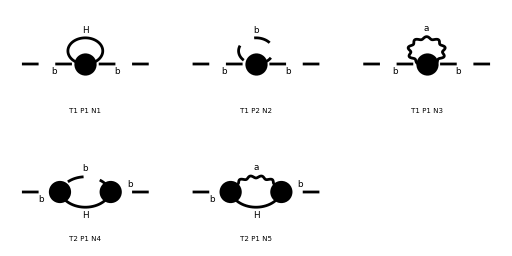

> Top. 1 ac/bc/0.m, 0 diagrams

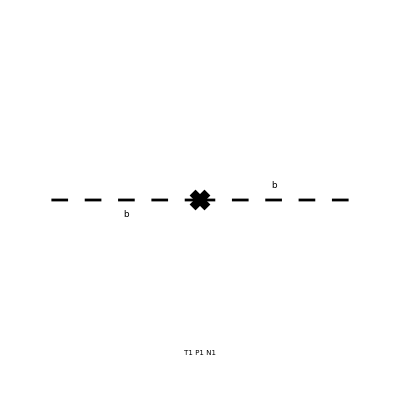

```mathematica
D1Lbb=diag[1,{S[2]},{S[2]}];
```

```mathematica
Amp1Lbb=D1Lbb//amp1L[{p1},{p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 2 Particles amplitudes

in total: 5 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-1/(16 π^4)ⅈ (e l^Lor1+e p1^Lor1) (-e l^Lor2-e p1^Lor2) (g^Lor1Lor2/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l-p1)^Lor1 (p1-l)^Lor2)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1)))))-(ⅈ g4^2 vev^2)/(64 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))-(ⅈ e^2 g^Lor1Lor2 (g^Lor1Lor2/(l^2-e^2 vev^2)-(l^Lor1 l^Lor2 (1-ξ_(V(1))))/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))))))/(16 π^4)-(3 ⅈ g4)/(64 π^4 (l^2-e^2 vev^2 ξ_(V(1))))-(ⅈ g4)/(64 π^4 (l^2-(g4 vev^2)/2)),-ⅈ (ⅈ p1^2 (Zb-1)-1/4 ⅈ vev^2 (-4 e^2 ξ_(V(1))+4 e^2 Zb Zmb^2 Zv^2 ξ_(V(1))+g4 Zb Zv^2-g4 Zb))}

```mathematica
Amp1LbbDiv=Amp1Lbb//amp1LSimplify[{Zb:> 1+Nd db,Zmb:> 1+Nd dmb,Zv:> 1+Nd dv},{SMP["Delta"],db,dmb,dv}]
```

-db e^2 vev^2 ξ_(V(1))+db p1^2-2 dmb e^2 vev^2 ξ_(V(1))-2 dv e^2 vev^2 ξ_(V(1))-1/2 dv g4 vev^2+(3 Δ e^4 vev^2)/(8 π^2)+(Δ e^2 g4 vev^2 ξ_(V(1)))/(32 π^2)-(3 Δ e^2 p1^2)/(8 π^2)+(Δ e^2 p1^2 ξ_(V(1)))/(8 π^2)+(3 Δ g4^2 vev^2)/(64 π^2)

```mathematica
dsol[6]=Solve[SelectNotFree2[Amp1LbbDiv/.dSub[db],p1]==0,db]//Flatten//Simplify
dSave[dsol[6]];
```

{db→-(Δ e^2 (ξ_(V(1))-3))/(8 π^2)}

```mathematica
dsol[7]=Solve[SelectFree2[Amp1LbbDiv/.dSub[dmb],p1]==0,dmb]//Flatten//Simplify
dSave[dsol[7]];
```

{dmb→-(3 Δ (8 e^4+2 e^2 g4+g4^2))/(32 π^2 g4)}

## One Loop c->c

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 1 Particles insertion

in total: 1 Particles insertion

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ac/bd/cdcd.m, 0 diagrams

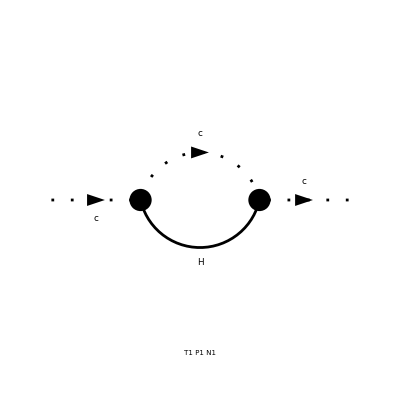

> Top. 1 ac/bc/0.m, 0 diagrams

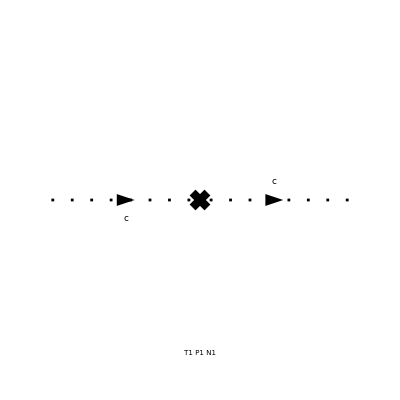

```mathematica
D1Lcc=diag[1,{U[1]},{U[1]}];
```

```mathematica
Amp1Lcc=D1Lcc//amp1L[{p1},{p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-(ⅈ e^4 vev^2 ξ_(V(1))^2)/(16 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1)))),-ⅈ (-ⅈ e^2 vev^2 ξ_(V(1)) (Zc Zmc^2 Zv^2-1)-ⅈ p1^2 (Zc-1))}

```mathematica
Amp1LccDiv=Amp1Lcc//amp1LSimplify[{Zc:> 1+Nd dc,Zmc:> 1+Nd dmc,Zv:> 1+Nd dv},{SMP["Delta"],dc,dmc,Zv}]
```

-dc e^2 vev^2 ξ_(V(1))-dc p1^2-2 dmc e^2 vev^2 ξ_(V(1))+(Δ e^4 vev^2 ξ_(V(1))^2)/(8 π^2)

```mathematica
dsol[8]=Solve[SelectNotFree2[Amp1LccDiv,p1]==0,dc]//Flatten//Simplify
dSave[dsol[8]];
```

{dc→0}

```mathematica
dsol[9]=Solve[SelectFree2[Amp1LccDiv/.dSub[dmc],p1]==0,dmc]//Flatten//Simplify
dSave[dsol[9]];
```

{dmc→(Δ e^2 ξ_(V(1)))/(16 π^2)}

## One Loop (2->1)

## One Loop H->HH

inserting at level(s) {Particles}

> Top. 1: 11 Particles insertions

> Top. 2: 3 Particles insertions

> Top. 3: 3 Particles insertions

> Top. 4: 3 Particles insertions

in total: 20 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bece/dede.m, 0 diagrams

> Top. 3 ad/becd/eded.m, 0 diagrams

> Top. 4 ad/bdce/eded.m, 0 diagrams

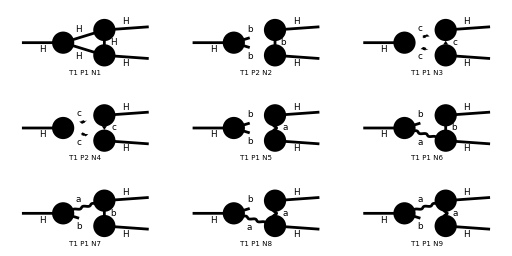

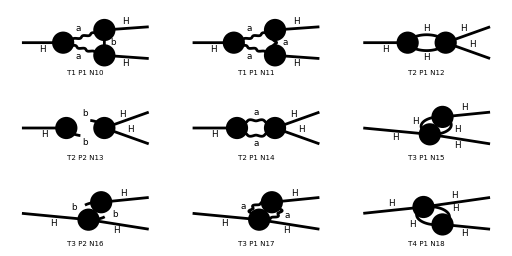

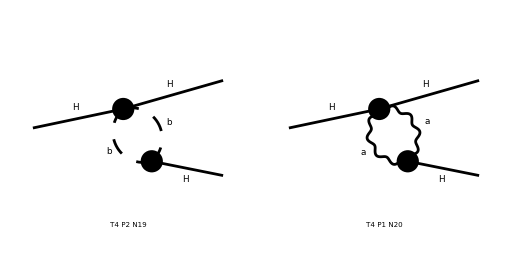

> Top. 1 ad/bdcd/0.m, 0 diagrams

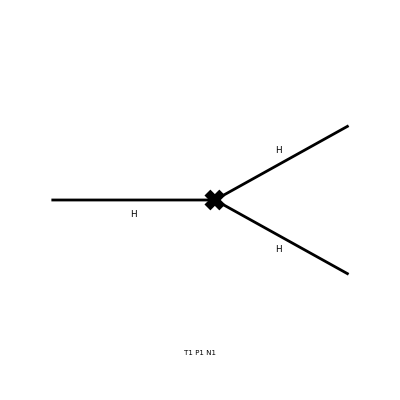

```mathematica
D1LHHH=diag[1,{S[1]},{S[1],S[1]}];
```

```mathematica
Amp1LHHH=D1LHHH//amp1L[{2p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 11 Particles amplitudes

> Top. 2: 3 Particles amplitudes

> Top. 3: 3 Particles amplitudes

> Top. 4: 3 Particles amplitudes

in total: 20 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{(ⅈ e^6 vev^3 ξ_(V(1))^3)/(8 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-1/(2 π^4)ⅈ vev^3 g^Lor1Lor3 g^Lor2Lor5 g^Lor4Lor6 (-(((1-ξ_(V(1)))^3 l^Lor1 l^Lor2 (l-2 p1)^Lor3 (2 p1-l)^Lor4 (p1-l)^Lor5 (l-p1)^Lor6)/(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-((1-ξ_(V(1)))^2 l^Lor1 l^Lor2 (l-2 p1)^Lor3 (2 p1-l)^Lor4 g^Lor5Lor6)/(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1)))-((1-ξ_(V(1)))^2 l^Lor1 l^Lor2 g^Lor3Lor4 (p1-l)^Lor5 (l-p1)^Lor6)/(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2)+((1-ξ_(V(1)))^2 g^Lor1Lor2 (l-2 p1)^Lor3 (2 p1-l)^Lor4 (p1-l)^Lor5 (l-p1)^Lor6)/(l^2-e^2 vev^2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1)))-((1-ξ_(V(1))) l^Lor1 l^Lor2 g^Lor3Lor4 g^Lor5Lor6)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2))+((1-ξ_(V(1))) g^Lor1Lor2 (l-2 p1)^Lor3 (2 p1-l)^Lor4 g^Lor5Lor6)/((l^2-e^2 vev^2).((l-p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) g^Lor1Lor2 g^Lor3Lor4 (p1-l)^Lor5 (l-p1)^Lor6)/((l^2-e^2 vev^2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2))+(g^Lor1Lor2 g^Lor3Lor4 g^Lor5Lor6)/((l^2-e^2 vev^2).((l-p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2))) e^6-1/(4 π^4)ⅈ vev g^Lor1Lor3 g^Lor2Lor4 (-((1-ξ_(V(1)))^2 l^Lor1 l^Lor2 (l+p1)^Lor3 (-l-p1)^Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l+p1)^2-e^2 vev^2).((l+p1)^2-e^2 vev^2 ξ_(V(1))))-((1-ξ_(V(1))) l^Lor1 l^Lor2 g^Lor3Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l+p1)^2-e^2 vev^2))+((1-ξ_(V(1))) g^Lor1Lor2 (l+p1)^Lor3 (-l-p1)^Lor4)/((l^2-e^2 vev^2).((l+p1)^2-e^2 vev^2).((l+p1)^2-e^2 vev^2 ξ_(V(1))))+(g^Lor1Lor2 g^Lor3Lor4)/((l^2-e^2 vev^2).((l+p1)^2-e^2 vev^2))) e^4-1/(8 π^4)ⅈ vev g^Lor1Lor3 g^Lor2Lor4 (-((1-ξ_(V(1)))^2 l^Lor1 l^Lor2 (l-2 p1)^Lor3 (2 p1-l)^Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-((1-ξ_(V(1))) l^Lor1 l^Lor2 g^Lor3Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2))+((1-ξ_(V(1))) g^Lor1Lor2 (l-2 p1)^Lor3 (2 p1-l)^Lor4)/((l^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))+(g^Lor1Lor2 g^Lor3Lor4)/((l^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2))) e^4-1/(8 π^4)ⅈ vev (-e l^Lor1-2 e p1^Lor1) g^Lor2Lor4 (e l^Lor3+e p1^Lor3) (((1-ξ_(V(1)))^2 (l-2 p1)^Lor1 (2 p1-l)^Lor2 (p1-l)^Lor3 (l-p1)^Lor4)/(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1)))+((1-ξ_(V(1))) (l-2 p1)^Lor1 (2 p1-l)^Lor2 g^Lor3Lor4)/(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1)))+((1-ξ_(V(1))) g^Lor1Lor2 (p1-l)^Lor3 (l-p1)^Lor4)/((l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2))+(g^Lor1Lor2 g^Lor3Lor4)/((l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2))) e^2-1/(8 π^4)ⅈ vev (e (l-2 p1)^Lor1-2 e p1^Lor1) g^Lor2Lor3 (-(((1-ξ_(V(1)))^2 l^Lor1 l^Lor2 (p1-l)^Lor3 (l-p1)^Lor4)/(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-((1-ξ_(V(1))) l^Lor1 l^Lor2 g^Lor3Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) g^Lor1Lor2 (p1-l)^Lor3 (l-p1)^Lor4)/((l^2-e^2 vev^2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))+(g^Lor1Lor2 g^Lor3Lor4)/((l^2-e^2 vev^2).((l-p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))) (e p1^Lor4+e (2 p1-l)^Lor4) e^2-1/(8 π^4)ⅈ vev g^Lor1Lor3 (e p1^Lor2+e (p1-l)^Lor2) (e (l-p1)^Lor4+e p1^Lor4) (-(((1-ξ_(V(1)))^2 l^Lor1 l^Lor2 (l-2 p1)^Lor3 (2 p1-l)^Lor4)/(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-((1-ξ_(V(1))) l^Lor1 l^Lor2 g^Lor3Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2))+((1-ξ_(V(1))) g^Lor1Lor2 (l-2 p1)^Lor3 (2 p1-l)^Lor4)/(l^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1)))+(g^Lor1Lor2 g^Lor3Lor4)/((l^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2))) e^2-(9 ⅈ g4^2 vev)/(128 π^4 (l^2-(g4 vev^2)/2).((l-2 p1)^2-(g4 vev^2)/2))-(9 ⅈ g4^2 vev)/(64 π^4 (l^2-(g4 vev^2)/2).((l+p1)^2-(g4 vev^2)/2))-(ⅈ g4^2 vev)/(128 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-(ⅈ g4^2 vev)/(64 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l+p1)^2-e^2 vev^2 ξ_(V(1))))-(27 ⅈ g4^3 vev^3)/(128 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-(g4 vev^2)/2))-(ⅈ g4^3 vev^3)/(128 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-1/(32 π^4)ⅈ g4 vev (e (l-2 p1)^Lor1-2 e p1^Lor1) (g^Lor1Lor2/((l^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-((1-ξ_(V(1))) l^Lor1 l^Lor2)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))) (e p1^Lor2+e (p1-l)^Lor2)-1/(32 π^4)ⅈ g4 vev (e l^Lor1+e p1^Lor1) (g^Lor1Lor2/((l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) (p1-l)^Lor1 (l-p1)^Lor2)/(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2 ξ_(V(1)))) (e p1^Lor2+e (2 p1-l)^Lor2)-1/(32 π^4)ⅈ g4 vev (-e l^Lor1-2 e p1^Lor1) (e (l-p1)^Lor2+e p1^Lor2) (g^Lor1Lor2/((l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l-2 p1)^Lor1 (2 p1-l)^Lor2)/(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1)))),-3/2 g4 vev (ZH^(3/2) ZHHH Zv-1)}

```mathematica
Amp1LHHHDiv=Amp1LHHH//amp1LSimplify[{ZHHH:> 1+Nd dHHH,ZH:> 1+Nd dH,Zv:> 1+Nd dv},{SMP["Delta"],dHHH,dH,dv},True]
```

Current diagram:       Number of diagrams: 16

Time: 33.7236 s

-(9 dH g4 vev)/4-(3 dHHH g4 vev)/2-(3 dv g4 vev)/2+(9 Δ e^4 vev)/(4 π^2)-(3 Δ e^2 g4 vev ξ_(V(1)))/(16 π^2)+(15 Δ g4^2 vev)/(32 π^2)

```mathematica
dsol[10]=Solve[SelectNotFree2[Amp1LHHHDiv/.dSub[dHHH],{SMP["Delta"],dHHH}]==0,dHHH]//Flatten//Simplify
dSave[dsol[10]];
```

{dHHH→(Δ (24 e^4-18 e^2 g4+7 g4^2))/(32 π^2 g4)}

## One Loop H->AA

inserting at level(s) {Particles}

> Top. 1: 6 Particles insertions

> Top. 2: 2 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 10 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bece/dede.m, 0 diagrams

> Top. 3 ad/becd/eded.m, 0 diagrams

> Top. 4 ad/bdce/eded.m, 0 diagrams

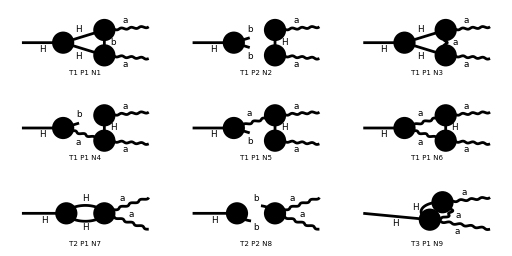

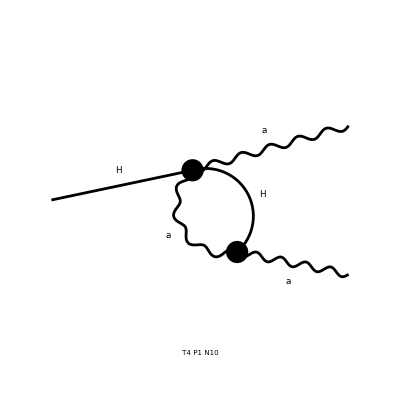

> Top. 1 ad/bdcd/0.m, 0 diagrams

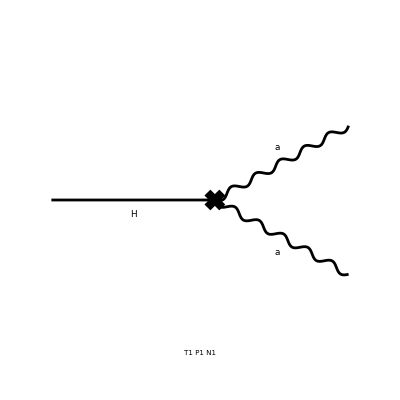

```mathematica
D1LHAA=diag[1,{S[1]},{V[1],V[1]}];
```

```mathematica
Amp1LHAA=D1LHAA//amp1L[{2p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 6 Particles amplitudes

> Top. 2: 2 Particles amplitudes

> Top. 3: 1 Particles amplitude

> Top. 4: 1 Particles amplitude

in total: 10 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{1/(2 π^4)ⅈ vev^3 g^Lor1Lor4 g^Lor2Lor6 g^Lor3Lor5 (-(((1-ξ_(V(1)))^2 l^Lor3 l^Lor4 (l-2 p1)^Lor5 (2 p1-l)^Lor6)/(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-((1-ξ_(V(1))) l^Lor3 l^Lor4 g^Lor5Lor6)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2))+((1-ξ_(V(1))) g^Lor3Lor4 (l-2 p1)^Lor5 (2 p1-l)^Lor6)/((l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))+(g^Lor3Lor4 g^Lor5Lor6)/((l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2))) e^6+1/(4 π^4)ⅈ vev g^Lor1Lor4 g^Lor2Lor3 (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l+p1)^Lor3 (-l-p1)^Lor4)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).((l+p1)^2-e^2 vev^2 ξ_(V(1))))) e^4+1/(4 π^4)ⅈ vev g^Lor1Lor3 g^Lor2Lor4 (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l+p1)^Lor3 (-l-p1)^Lor4)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).((l+p1)^2-e^2 vev^2 ξ_(V(1))))) e^4+1/(8 π^4)3 ⅈ g4 vev^3 g^Lor1Lor3 g^Lor2Lor4 (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-2 p1)^2-(g4 vev^2)/2))+((1-ξ_(V(1))) (p1-l)^Lor3 (l-p1)^Lor4)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-(g4 vev^2)/2))) e^4+(3 ⅈ e^2 g4 vev g^Lor1Lor2)/(32 π^4 (l^2-(g4 vev^2)/2).((l-2 p1)^2-(g4 vev^2)/2))+(ⅈ e^2 g4 vev g^Lor1Lor2)/(32 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))+1/(8 π^4)ⅈ vev g^Lor1Lor4 (e (p1-l)^Lor2+e (2 p1-l)^Lor2) (e (l-2 p1)^Lor3-2 e p1^Lor3) (g^Lor3Lor4/((l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))) e^2+1/(8 π^4)ⅈ vev (e l^Lor1+e (l-p1)^Lor1) g^Lor2Lor4 (-e l^Lor3-2 e p1^Lor3) (g^Lor3Lor4/((l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l-2 p1)^Lor3 (2 p1-l)^Lor4)/(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1)))) e^2+(3 ⅈ g4 vev (e (p1-l)^Lor1-e l^Lor1) (e (l-2 p1)^Lor2+e (l-p1)^Lor2))/(32 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-(g4 vev^2)/2))+(ⅈ g4 vev (e l^Lor1+e (l-p1)^Lor1) (e (p1-l)^Lor2+e (2 p1-l)^Lor2))/(32 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1)))),2 e^2 vev (ZA ZAAH √ZH Zv-1) g^Lor1Lor2}

```mathematica
Amp1LHAADiv=Amp1LHAA//amp1LSimplify[{ZAAH:> 1+Nd dAAH,ZA:> 1+Nd dA,ZH:> 1+Nd dH,Zv:> 1+Nd dv},{SMP["Delta"],dAAH,dA,dH,dv},True]
```

Current diagram:       Number of diagrams: 10

Time: 24.3786 s

2 dA e^2 vev g^Lor1Lor2+2 dAAH e^2 vev g^Lor1Lor2+dH e^2 vev g^Lor1Lor2+2 dv e^2 vev g^Lor1Lor2-(3 Δ e^4 vev g^Lor1Lor2)/(4 π^2)

```mathematica
dsol[11]=Solve[SelectNotFree2[Amp1LHAADiv/.dSub[dAAH],{SMP["Delta"],dAAH}]==0,dAAH]//Flatten//Simplify
dSave[dsol[11]];
```

{dAAH→-(Δ (72 e^4-22 e^2 g4+9 g4^2))/(96 π^2 g4)}

## One Loop H->bb

inserting at level(s) {Particles}

> Top. 1: 6 Particles insertions

> Top. 2: 3 Particles insertions

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 11 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bece/dede.m, 0 diagrams

> Top. 3 ad/becd/eded.m, 0 diagrams

> Top. 4 ad/bdce/eded.m, 0 diagrams

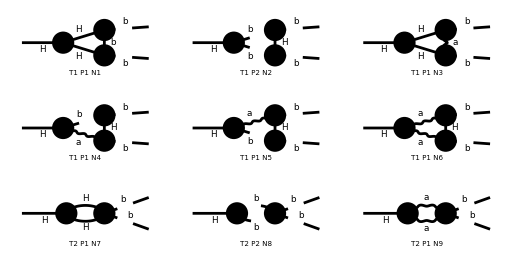

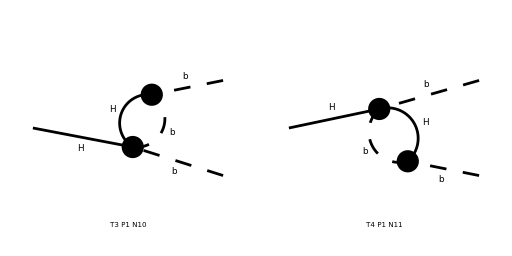

> Top. 1 ad/bdcd/0.m, 0 diagrams

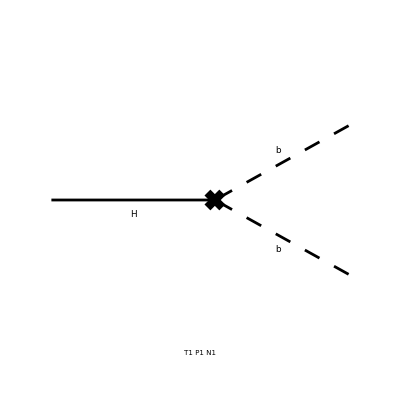

```mathematica
D1LHbb=diag[1,{S[1]},{S[2],S[2]}];
```

```mathematica
Amp1LHbb=D1LHbb//amp1L[{2p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 6 Particles amplitudes

> Top. 2: 3 Particles amplitudes

> Top. 3: 1 Particles amplitude

> Top. 4: 1 Particles amplitude

in total: 11 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{-1/(8 π^4)ⅈ vev g^Lor1Lor3 g^Lor2Lor4 (-((1-ξ_(V(1)))^2 l^Lor1 l^Lor2 (l-2 p1)^Lor3 (2 p1-l)^Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-((1-ξ_(V(1))) l^Lor1 l^Lor2 g^Lor3Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2))+((1-ξ_(V(1))) g^Lor1Lor2 (l-2 p1)^Lor3 (2 p1-l)^Lor4)/((l^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))+(g^Lor1Lor2 g^Lor3Lor4)/((l^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2))) e^4-1/(8 π^4)ⅈ vev g^Lor1Lor3 (e (l-p1)^Lor2-e p1^Lor2) (e (p1-l)^Lor4-e p1^Lor4) (-(((1-ξ_(V(1)))^2 l^Lor1 l^Lor2 (l-2 p1)^Lor3 (2 p1-l)^Lor4)/(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-((1-ξ_(V(1))) l^Lor1 l^Lor2 g^Lor3Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2))+((1-ξ_(V(1))) g^Lor1Lor2 (l-2 p1)^Lor3 (2 p1-l)^Lor4)/((l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))+(g^Lor1Lor2 g^Lor3Lor4)/((l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2))) e^2-(3 ⅈ g4^2 vev)/(128 π^4 (l^2-(g4 vev^2)/2).((l-2 p1)^2-(g4 vev^2)/2))-(ⅈ g4^2 vev)/(32 π^4 (l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2 ξ_(V(1))))-(3 ⅈ g4^2 vev)/(128 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-(3 ⅈ g4^3 vev^3)/(128 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-(g4 vev^2)/2))-(ⅈ g4^3 vev^3)/(128 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-1/(32 π^4)3 ⅈ g4 vev (-e l^Lor1-e p1^Lor1) (g^Lor1Lor2/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-2 p1)^2-(g4 vev^2)/2))+((1-ξ_(V(1))) (p1-l)^Lor1 (l-p1)^Lor2)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-(g4 vev^2)/2))) (e (l-2 p1)^Lor2-e p1^Lor2)-1/(32 π^4)ⅈ g4 vev (e (l-2 p1)^Lor1-2 e p1^Lor1) (g^Lor1Lor2/((l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-((1-ξ_(V(1))) l^Lor1 l^Lor2)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))) (e (l-p1)^Lor2-e p1^Lor2)-1/(32 π^4)ⅈ g4 vev (-e l^Lor1-2 e p1^Lor1) (e (p1-l)^Lor2-e p1^Lor2) (g^Lor1Lor2/((l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l-2 p1)^Lor1 (2 p1-l)^Lor2)/(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1)))),-1/2 g4 vev (Zb ZbbH √ZH Zv-1)}

```mathematica
Amp1LHbbDiv=Amp1LHbb//amp1LSimplify[{ZbbH:> 1+Nd dbbH,Zb:> 1+Nd db,ZH:> 1+Nd dH,Zv:> 1+Nd dv},{SMP["Delta"],dbbH,db,dH,dv},True]
```

Current diagram:       Number of diagrams: 10

Time: 11.227 s

-(db g4 vev)/2-(dbbH g4 vev)/2-(dH g4 vev)/4-(dv g4 vev)/2+(3 Δ e^4 vev)/(4 π^2)-(Δ e^2 g4 vev ξ_(V(1)))/(16 π^2)+(5 Δ g4^2 vev)/(32 π^2)

```mathematica
dsol[12]=Solve[SelectNotFree2[Amp1LHbbDiv/.dSub[dbbH],{SMP["Delta"],dbbH}]==0,dbbH]//Flatten//Simplify
dSave[dsol[12]];
```

{dbbH→(Δ (24 e^4-18 e^2 g4+7 g4^2))/(32 π^2 g4)}

## One Loop H->Ab

inserting at level(s) {Particles}

> Top. 1: 6 Particles insertions

> Top. 2: 1 Particles insertion

> Top. 3: 1 Particles insertion

> Top. 4: 1 Particles insertion

in total: 9 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ad/becf/dedfef.m, 0 diagrams

> Top. 2 ad/bece/dede.m, 0 diagrams

> Top. 3 ad/becd/eded.m, 0 diagrams

> Top. 4 ad/bdce/eded.m, 0 diagrams

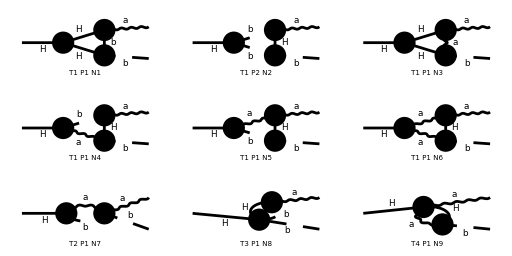

> Top. 1 ad/bdcd/0.m, 0 diagrams

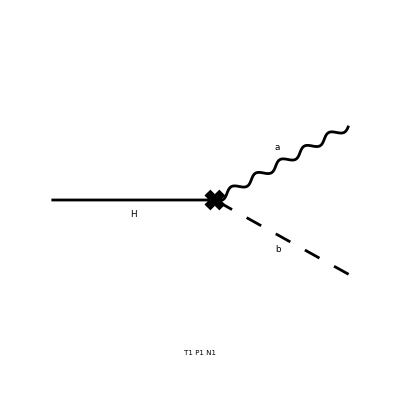

```mathematica
D1LHAb=diag[1,{S[1]},{V[1],S[2]} ];
```

```mathematica
Amp1LHAb=D1LHAb//amp1L[{2p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 6 Particles amplitudes

> Top. 2: 1 Particles amplitude

> Top. 3: 1 Particles amplitude

> Top. 4: 1 Particles amplitude

in total: 9 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{1/(4 π^4)vev^2 g^Lor1Lor3 g^Lor2Lor4 (e (p1-l)^Lor5-e p1^Lor5) (-(((1-ξ_(V(1)))^2 l^Lor2 l^Lor3 (l-2 p1)^Lor4 (2 p1-l)^Lor5)/(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-((1-ξ_(V(1))) l^Lor2 l^Lor3 g^Lor4Lor5)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2))+((1-ξ_(V(1))) g^Lor2Lor3 (l-2 p1)^Lor4 (2 p1-l)^Lor5)/((l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))+(g^Lor2Lor3 g^Lor4Lor5)/((l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2))) e^4+1/(16 π^4)g4 vev^2 g^Lor1Lor3 (e (l-2 p1)^Lor2-2 e p1^Lor2) (g^Lor2Lor3/((l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))-((1-ξ_(V(1))) l^Lor2 l^Lor3)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))) e^2+1/(8 π^4)g^Lor1Lor3 (e l^Lor2-e p1^Lor2) (g^Lor2Lor3/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l+p1)^Lor2 (-l-p1)^Lor3)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).((l+p1)^2-e^2 vev^2 ξ_(V(1))))) e^2+1/(16 π^4)3 g4 vev^2 g^Lor1Lor2 (g^Lor2Lor3/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-2 p1)^2-(g4 vev^2)/2))+((1-ξ_(V(1))) (p1-l)^Lor2 (l-p1)^Lor3)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-(g4 vev^2)/2))) (e (l-2 p1)^Lor3-e p1^Lor3) e^2+1/(8 π^4)g^Lor1Lor3 (-e l^Lor2-2 e p1^Lor2) (g^Lor2Lor3/((l^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l-2 p1)^Lor2 (2 p1-l)^Lor3)/((l^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))) e^2+(g4^2 vev^2 (e l^Lor1+e (l-p1)^Lor1))/(64 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))+(3 g4^2 vev^2 (e (p1-l)^Lor1-e l^Lor1))/(64 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-(g4 vev^2)/2))+(g4 (e l^Lor1+e (l+p1)^Lor1))/(32 π^4 (l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2 ξ_(V(1))))+1/(16 π^4)(e l^Lor1+e (l-p1)^Lor1) (-e l^Lor2-2 e p1^Lor2) (e (p1-l)^Lor3-e p1^Lor3) (g^Lor2Lor3/((l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l-2 p1)^Lor2 (2 p1-l)^Lor3)/(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1)))),3 ⅈ e (ZAbH √(ZA Zb ZH)-1) p1^Lor1}

```mathematica
Amp1LHAbDiv=Amp1LHAb//amp1LSimplify[{ZAbH:> 1+Nd dAbH,ZA:> 1+Nd dA,Zb:> 1+Nd db,ZH:> 1+Nd dH},{SMP["Delta"],dAbH,dA,db,dH},True]
```

Current diagram:       Number of diagrams: 9

Time: 13.9517 s

3/2 ⅈ dA e p1^Lor1+3 ⅈ dAbH e p1^Lor1+3/2 ⅈ db e p1^Lor1+3/2 ⅈ dH e p1^Lor1-(9 ⅈ Δ e^3 p1^Lor1)/(8 π^2)+(3 ⅈ Δ e^3 p1^Lor1 ξ_(V(1)))/(8 π^2)

```mathematica
dsol[13]=Solve[SelectNotFree2[Amp1LHAbDiv/.dSub[dAbH],{SMP["Delta"],dAbH}]==0,dAbH]//Flatten//Simplify
dSave[dsol[13]];
```

{dAbH→(Δ e^2)/(48 π^2)}

## One Loop H->cc

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 0 Particles insertions

> Top. 3: 0 Particles insertions

> Top. 4: 0 Particles insertions

in total: 2 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 ad/becf/dedfef.m, 0 diagrams

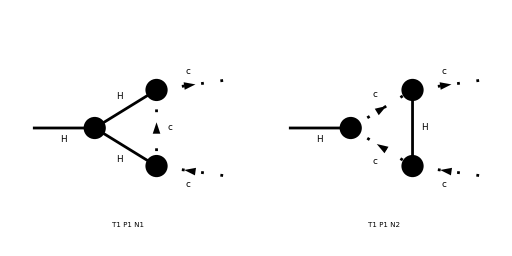

> Top. 1 ad/bdcd/0.m, 0 diagrams

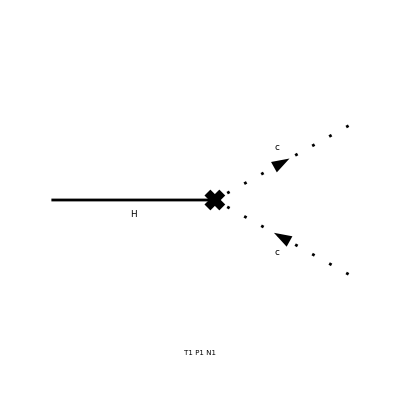

```mathematica
D1LHcc=diag[1,{S[1]},{U[1],-U[1]} ];
```

```mathematica
Amp1LHcc=D1LHcc//amp1L[{2p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

in total: 2 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{(ⅈ e^6 vev^3 ξ_(V(1))^3)/(16 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))+(3 ⅈ e^4 g4 vev^3 ξ_(V(1))^2)/(32 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-(g4 vev^2)/2)),e^2 vev ξ_(V(1)) (Zc ZccH √ZH Zv-1)}

```mathematica
Amp1LHccDiv=Amp1LHcc//amp1LSimplify[{ZccH:> 1+Nd dccH,Zc:> 1+Nd dc,ZH:> 1+Nd dH,Zv:> 1+Nd dv},{SMP["Delta"],dccH,dc,dH,dv},True]
```

Current diagram:       Number of diagrams: 2

Time: 0.713667 s

dc e^2 vev ξ_(V(1))+dccH e^2 vev ξ_(V(1))+1/2 dH e^2 vev ξ_(V(1))+dv e^2 vev ξ_(V(1))

```mathematica
dsol[14]=Solve[SelectNotFree2[Amp1LHccDiv/.dSub[dccH],{SMP["Delta"],dccH}]==0,dccH]//Flatten//Simplify
dSave[dsol[14]];
```

{dccH→-(3 Δ (8 e^4+2 e^2 g4+g4^2))/(32 π^2 g4)}

## One Loop (2->2)

## One Loop HH->HH

inserting at level(s) {Particles}

> Top. 1: 5 Particles insertions

> Top. 2: 5 Particles insertions

> Top. 3: 5 Particles insertions

> Top. 4: 5 Particles insertions

> Top. 5: 5 Particles insertions

> Top. 6: 5 Particles insertions

> Top. 7: 19 Particles insertions

> Top. 8: 19 Particles insertions

> Top. 9: 19 Particles insertions

> Top. 10: 3 Particles insertions

> Top. 11: 3 Particles insertions

> Top. 12: 3 Particles insertions

in total: 96 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 8 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 9 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 10 aebe/cfdf/efef.m, 0 diagrams

> Top. 11 aebf/cedf/efef.m, 0 diagrams

> Top. 12 aebf/cfde/efef.m, 0 diagrams

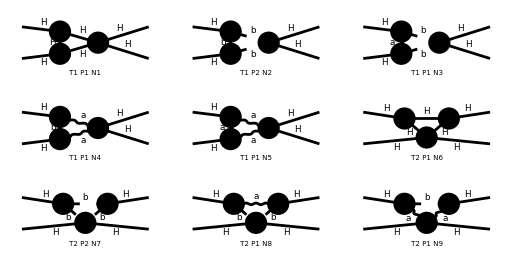

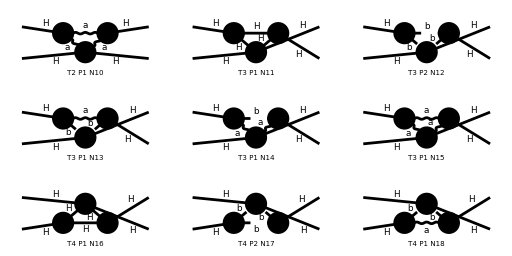

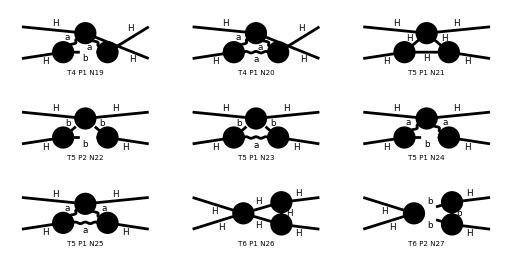

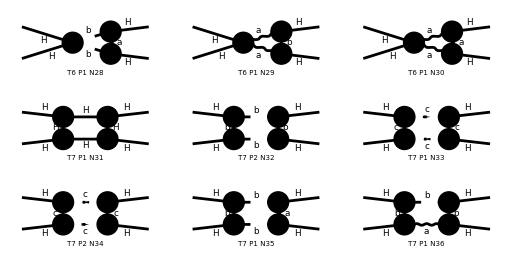

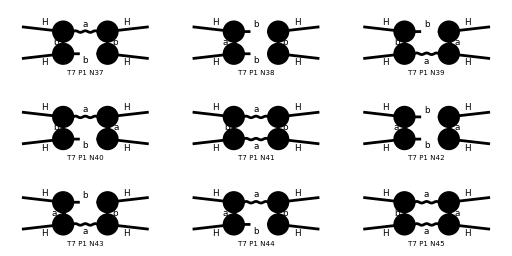

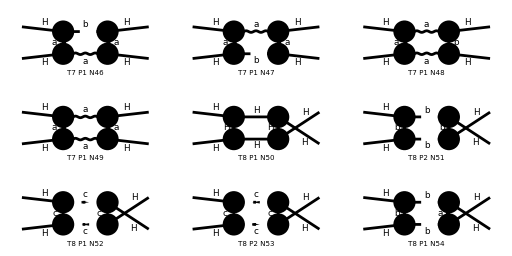

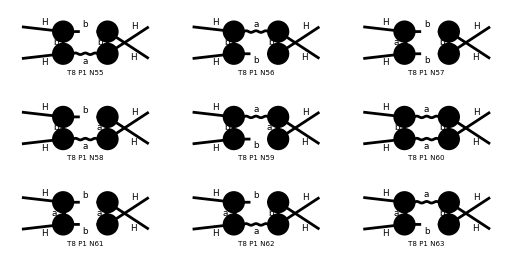

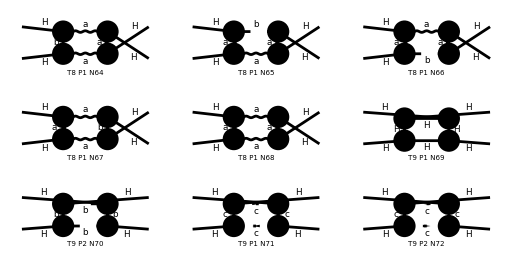

> Top. 1 aebe/cede/0.m, 0 diagrams

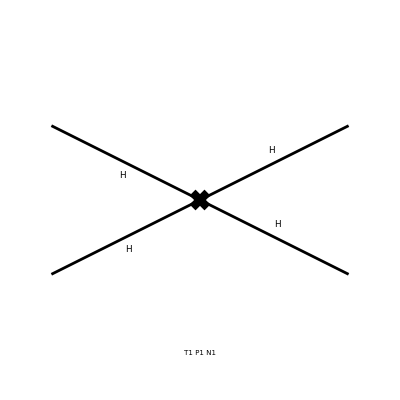

```mathematica
D1LHHHH=diag[1,{S[1],S[1]},{S[1],S[1]}];
```

```mathematica
Amp1LHHHH=D1LHHHH//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 5 Particles amplitudes

> Top. 2: 5 Particles amplitudes

> Top. 3: 5 Particles amplitudes

> Top. 4: 5 Particles amplitudes

> Top. 5: 5 Particles amplitudes

> Top. 6: 5 Particles amplitudes

> Top. 7: 19 Particles amplitudes

> Top. 8: 19 Particles amplitudes

> Top. 9: 19 Particles amplitudes

> Top. 10: 3 Particles amplitudes

> Top. 11: 3 Particles amplitudes

> Top. 12: 3 Particles amplitudes

in total: 96 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{(ⅈ e^8 vev^4 ξ_(V(1))^4)/(8 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+127,-3/2 g4 (ZH^2 ZHHHH-1)}
 |  |  |  |

```mathematica
Amp1LHHHHDiv=Amp1LHHHH//amp1LSimplify[{ZHHHH:> 1+Nd dHHHH,ZH:> 1+Nd dH},{SMP["Delta"],dHHHH,dH},True]
```

Current diagram:       Number of diagrams: 65

Time: 452.013 s

-3 dH g4-(3 dHHHH g4)/2+(9 Δ e^4)/(4 π^2)-(3 Δ e^2 g4 ξ_(V(1)))/(8 π^2)+(15 Δ g4^2)/(32 π^2)

```mathematica
dsol[15]=Solve[SelectNotFree2[Amp1LHHHHDiv/.dSub[dHHHH],{SMP["Delta"],dHHHH}]==0,dHHHH]//Flatten//Simplify
dSave[dsol[15]];
```

{dHHHH→(Δ (24 e^4-12 e^2 g4+5 g4^2))/(16 π^2 g4)}

## One Loop Hb->Hb

inserting at level(s) {Particles}

> Top. 1: 3 Particles insertions

> Top. 2: 5 Particles insertions

> Top. 3: 3 Particles insertions

> Top. 4: 3 Particles insertions

> Top. 5: 4 Particles insertions

> Top. 6: 3 Particles insertions

> Top. 7: 10 Particles insertions

> Top. 8: 8 Particles insertions

> Top. 9: 10 Particles insertions

> Top. 10: 1 Particles insertion

> Top. 11: 3 Particles insertions

> Top. 12: 1 Particles insertion

in total: 54 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 8 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 9 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 10 aebe/cfdf/efef.m, 0 diagrams

> Top. 11 aebf/cedf/efef.m, 0 diagrams

> Top. 12 aebf/cfde/efef.m, 0 diagrams

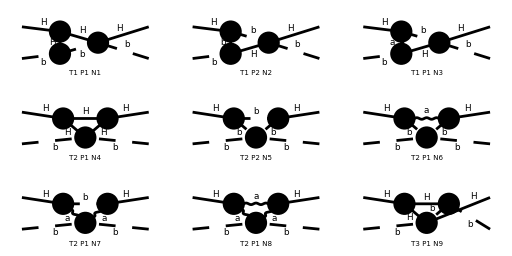

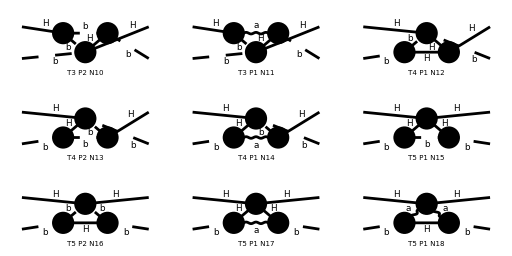

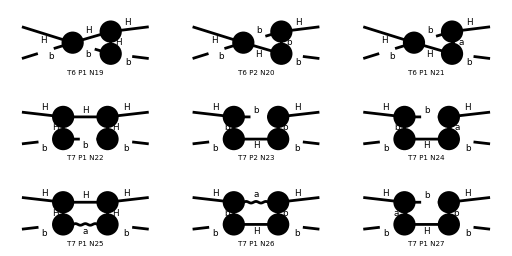

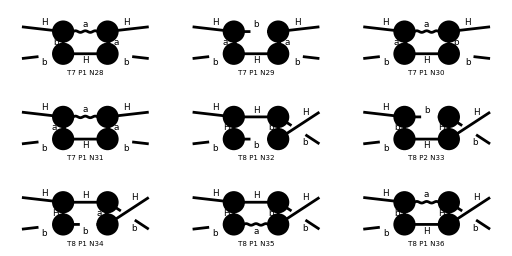

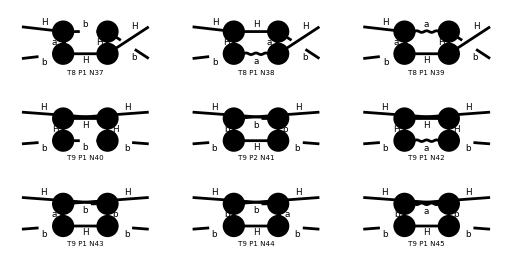

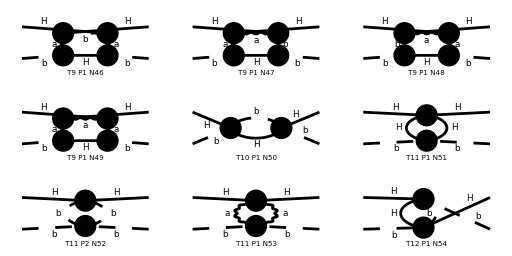

> Top. 1 aebe/cede/0.m, 0 diagrams

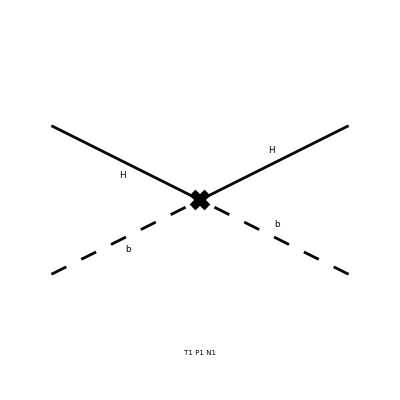

```mathematica
D1LHbHb=diag[1,{S[1],S[2]},{S[1],S[2]}];
```

```mathematica
Amp1LHbHb=D1LHbHb//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 5 Particles amplitudes

> Top. 3: 3 Particles amplitudes

> Top. 4: 3 Particles amplitudes

> Top. 5: 4 Particles amplitudes

> Top. 6: 3 Particles amplitudes

> Top. 7: 10 Particles amplitudes

> Top. 8: 8 Particles amplitudes

> Top. 9: 10 Particles amplitudes

> Top. 10: 1 Particles amplitude

> Top. 11: 3 Particles amplitudes

> Top. 12: 1 Particles amplitude

in total: 54 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{1,-1/2 g4 (Zb ZbbHH ZH-1)}
 |  |  |  |

```mathematica
Amp1LHbHbDiv=Amp1LHbHb//amp1LSimplify[{ZbbHH:> 1+Nd dbbHH,ZH:> 1+Nd dH,Zb:> 1+Nd db},{SMP["Delta"],dbbHH,dH,db},True]
```

Current diagram:       Number of diagrams: 52

Time: 171.403 s

-(db g4)/2-(dbbHH g4)/2-(dH g4)/2+(3 Δ e^4)/(4 π^2)-(Δ e^2 g4 ξ_(V(1)))/(8 π^2)+(5 Δ g4^2)/(32 π^2)

```mathematica
dsol[16]=Solve[SelectNotFree2[Amp1LHbHbDiv/.dSub[dbbHH],{SMP["Delta"],dbbHH}]==0,dbbHH]//Flatten//Simplify
dSave[dsol[16]];
```

{dbbHH→(Δ (24 e^4-12 e^2 g4+5 g4^2))/(16 π^2 g4)}

## One Loop Ab->Ab

inserting at level(s) {Particles}

> Top. 1: 2 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 2 Particles insertions

> Top. 4: 2 Particles insertions

> Top. 5: 3 Particles insertions

> Top. 6: 2 Particles insertions

> Top. 7: 8 Particles insertions

> Top. 8: 8 Particles insertions

> Top. 9: 8 Particles insertions

> Top. 10: 1 Particles insertion

> Top. 11: 2 Particles insertions

> Top. 12: 1 Particles insertion

in total: 43 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 8 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 9 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 10 aebe/cfdf/efef.m, 0 diagrams

> Top. 11 aebf/cedf/efef.m, 0 diagrams

> Top. 12 aebf/cfde/efef.m, 0 diagrams

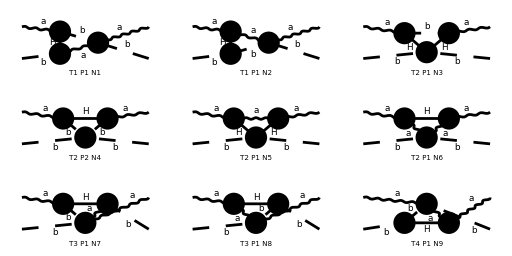

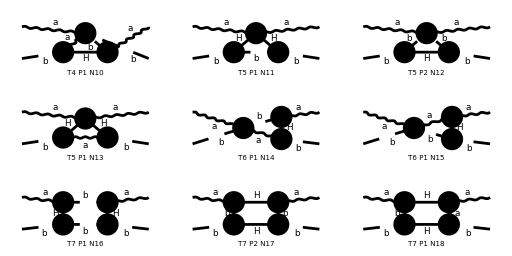

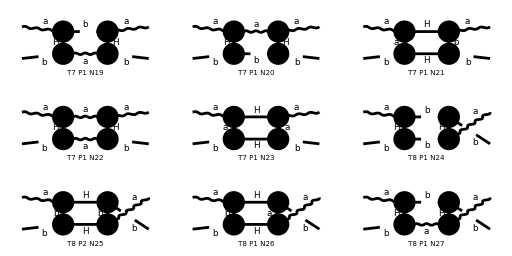

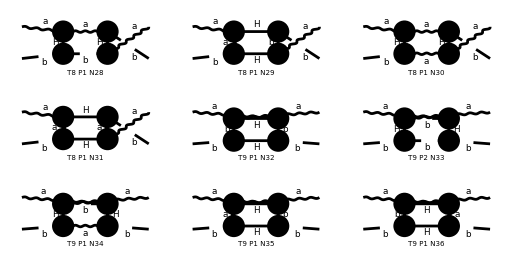

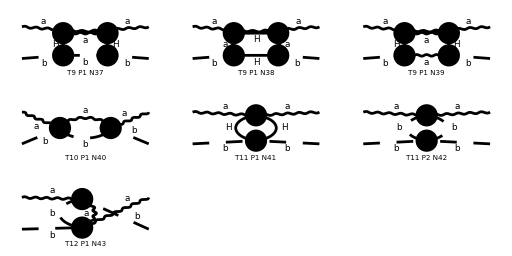

> Top. 1 aebe/cede/0.m, 0 diagrams

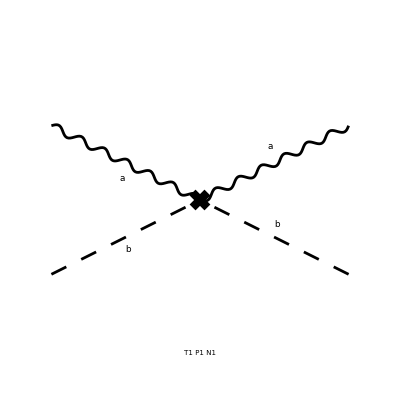

```mathematica
D1LAbAb=diag[1,{V[1],S[2]},{V[1],S[2]}];
```

```mathematica
Amp1LAbAb=D1LAbAb//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 2 Particles amplitudes

> Top. 2: 4 Particles amplitudes

> Top. 3: 2 Particles amplitudes

> Top. 4: 2 Particles amplitudes

> Top. 5: 3 Particles amplitudes

> Top. 6: 2 Particles amplitudes

> Top. 7: 8 Particles amplitudes

> Top. 8: 8 Particles amplitudes

> Top. 9: 8 Particles amplitudes

> Top. 10: 1 Particles amplitude

> Top. 11: 2 Particles amplitudes

> Top. 12: 1 Particles amplitude

in total: 43 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{1/(2 π^4)ⅈ vev^2 g^Lor1Lor3 g^Lor2Lor5 g^Lor4Lor6 (((1-ξ_(V(1)))^2 (l-p1)^Lor3 (p1-l)^Lor4 (p1-l)^Lor5 (l-p1)^Lor6)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4 g^Lor5Lor6)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2)^2.((l-p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) g^Lor3Lor4 (p1-l)^Lor5 (l-p1)^Lor6)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2))+(g^Lor3Lor4 g^Lor5Lor6)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2)^2)) e^6+(ⅈ g^Lor1Lor3 g^Lor2Lor4 (g^Lor3Lor4/((l^2-e^2 vev^2 ξ_(V(1))).(l^2-e^2 vev^2))-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2-e^2 vev^2 ξ_(V(1))).(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))))) e^4)/(4 π^4)+(ⅈ g4 vev^2 g^Lor1Lor3 g^Lor2Lor4 (g^Lor3Lor4/((l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2)^2)-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2)^2)) e^4)/(8 π^4)+(ⅈ g4^2 vev^4 g^Lor1Lor3 g^Lor2Lor4 (g^Lor3Lor4/((l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))) e^4)/(16 π^4)+(ⅈ g4 vev^2 g^Lor1Lor4 g^Lor2Lor3 (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) (l+p1)^Lor3 (-l-p1)^Lor4)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2 ξ_(V(1))))) e^4)/(8 π^4)+(ⅈ g4 vev^2 g^Lor1Lor4 g^Lor2Lor3 (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (p1-l)^Lor3 (l-p1)^Lor4)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))) e^4)/(8 π^4)+(ⅈ g4 vev^2 g^Lor1Lor3 g^Lor2Lor4 (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))) e^4)/(8 π^4)+(ⅈ g4 vev^2 g^Lor1Lor3 g^Lor2Lor4 (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))) e^4)/(8 π^4)+(ⅈ g4^2 vev^4 g^Lor1Lor3 g^Lor2Lor4 (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))) e^4)/(16 π^4)+(ⅈ g^Lor1Lor3 g^Lor2Lor4 (g^Lor3Lor4/((l^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l-2 p1)^Lor3 (2 p1-l)^Lor4)/((l^2-e^2 vev^2 ξ_(V(1))).((l-2 p1)^2-e^2 vev^2).((l-2 p1)^2-e^2 vev^2 ξ_(V(1))))) e^4)/(4 π^4)+1/(4 π^4)ⅈ vev^2 g^Lor1Lor3 g^Lor2Lor5 (e p1^Lor4+e (l+p1)^Lor4) (((1-ξ_(V(1)))^2 l^Lor3 l^Lor4 l^Lor5 l^Lor6)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))-((1-ξ_(V(1))) l^Lor3 l^Lor4 g^Lor5Lor6)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2))-((1-ξ_(V(1))) g^Lor3Lor4 l^Lor5 l^Lor6)/((l^2-e^2 vev^2).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))+(g^Lor3Lor4 g^Lor5Lor6)/((l^2-e^2 vev^2).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2))) (e (-l-p1)^Lor6-e p1^Lor6) e^4+1/(4 π^4)ⅈ vev^2 g^Lor1Lor3 g^Lor2Lor4 (e p1^Lor5+e (p1-l)^Lor5) (((1-ξ_(V(1)))^2 l^Lor3 l^Lor4 l^Lor5 l^Lor6)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))-((1-ξ_(V(1))) l^Lor3 l^Lor4 g^Lor5Lor6)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2))-((1-ξ_(V(1))) g^Lor3Lor4 l^Lor5 l^Lor6)/((l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))+(g^Lor3Lor4 g^Lor5Lor6)/((l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2))) (e (l-p1)^Lor6-e p1^Lor6) e^4+1/(4 π^4)ⅈ vev^2 g^Lor1Lor3 g^Lor2Lor5 (e p1^Lor4+e (l+p1)^Lor4) (((1-ξ_(V(1)))^2 l^Lor3 l^Lor4 l^Lor5 l^Lor6)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))-((1-ξ_(V(1))) l^Lor3 l^Lor4 g^Lor5Lor6)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2))-((1-ξ_(V(1))) g^Lor3Lor4 l^Lor5 l^Lor6)/((l^2-e^2 vev^2).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))+(g^Lor3Lor4 g^Lor5Lor6)/((l^2-e^2 vev^2).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2))) (e (l-p1)^Lor6-e p1^Lor6) e^4+1/(4 π^4)ⅈ vev^2 g^Lor1Lor3 g^Lor2Lor6 (-e l^Lor4-e p1^Lor4) (e l^Lor5+e p1^Lor5) (((1-ξ_(V(1)))^2 (l-p1)^Lor3 (p1-l)^Lor4 (l-p1)^Lor5 (p1-l)^Lor6)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4 g^Lor5Lor6)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) g^Lor3Lor4 (l-p1)^Lor5 (p1-l)^Lor6)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2))+(g^Lor3Lor4 g^Lor5Lor6)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2))) e^4+1/(4 π^4)ⅈ vev^2 g^Lor1Lor3 g^Lor2Lor6 (-e l^Lor4-e p1^Lor4) (e p1^Lor5-e l^Lor5) (((1-ξ_(V(1)))^2 (l-p1)^Lor3 (p1-l)^Lor4 (-l-p1)^Lor5 (l+p1)^Lor6)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4 g^Lor5Lor6)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) g^Lor3Lor4 (-l-p1)^Lor5 (l+p1)^Lor6)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2))+(g^Lor3Lor4 g^Lor5Lor6)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2))) e^4+1/(4 π^4)ⅈ vev^2 g^Lor1Lor3 g^Lor2Lor4 (e p1^Lor5-e l^Lor5) (e l^Lor6-e p1^Lor6) (((1-ξ_(V(1)))^2 (l-p1)^Lor3 (p1-l)^Lor4 (-l-p1)^Lor5 (l+p1)^Lor6)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4 g^Lor5Lor6)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) g^Lor3Lor4 (-l-p1)^Lor5 (l+p1)^Lor6)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2))+(g^Lor3Lor4 g^Lor5Lor6)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2))) e^4+(ⅈ e^2 g4 g^Lor1Lor2)/(32 π^4 (l^2-(g4 vev^2)/2)^2)+(3 ⅈ e^2 g4 g^Lor1Lor2)/(32 π^4 (l^2-e^2 vev^2 ξ_(V(1)))^2)+(ⅈ e^2 g4^2 vev^2 g^Lor1Lor2)/(32 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1)))^2)+(ⅈ e^2 g4^2 vev^2 g^Lor1Lor2)/(32 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2)^2)+(ⅈ (e l^Lor1+e (l-p1)^Lor1) g^Lor2Lor4 (-e l^Lor3-e p1^Lor3) (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) (p1-l)^Lor3 (l-p1)^Lor4)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1)))^2)) e^2)/(8 π^4)+(ⅈ g^Lor1Lor4 (e l^Lor2+e (l+p1)^Lor2) (-e l^Lor3-e p1^Lor3) (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (p1-l)^Lor3 (l-p1)^Lor4)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))) e^2)/(8 π^4)+(ⅈ g4 vev^2 (e (p1-l)^Lor1-e l^Lor1) g^Lor2Lor3 (g^Lor3Lor4/((l^2-e^2 vev^2 ξ_(V(1))).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2))-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2-e^2 vev^2 ξ_(V(1))).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))) (e (-l-p1)^Lor4-e p1^Lor4) e^2)/(16 π^4)+(ⅈ g^Lor1Lor2 (e p1^Lor3+e (p1-l)^Lor3) (g^Lor3Lor4/((l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2)^2)-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2)^2)) (e (l-p1)^Lor4-e p1^Lor4) e^2)/(8 π^4)+(ⅈ g4 vev^2 (e (p1-l)^Lor1-e l^Lor1) g^Lor2Lor3 (g^Lor3Lor4/((l^2-e^2 vev^2 ξ_(V(1))).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2))-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2-e^2 vev^2 ξ_(V(1))).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))) (e (l-p1)^Lor4-e p1^Lor4) e^2)/(16 π^4)+(ⅈ g^Lor1Lor4 (e (p1-l)^Lor2-e l^Lor2) (e l^Lor3+e p1^Lor3) (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1)))^2)) e^2)/(8 π^4)+(ⅈ g4 vev^2 (e l^Lor1+e (l-p1)^Lor1) g^Lor2Lor4 (e l^Lor3+e p1^Lor3) (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))) e^2)/(16 π^4)+(ⅈ g4 vev^2 g^Lor1Lor3 (e (p1-l)^Lor2-e l^Lor2) (-e l^Lor4-e p1^Lor4) (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))) e^2)/(16 π^4)+(ⅈ g4 vev^2 g^Lor1Lor3 (e l^Lor2+e (l+p1)^Lor2) (-e l^Lor4-e p1^Lor4) (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2))+((1-ξ_(V(1))) (l-p1)^Lor3 (p1-l)^Lor4)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))) e^2)/(16 π^4)+(ⅈ g4 vev^2 g^Lor1Lor3 (e (-l-p1)^Lor2-e l^Lor2) (g^Lor3Lor4/((l^2-e^2 vev^2).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))) (e p1^Lor4+e (l+p1)^Lor4) e^2)/(16 π^4)+(ⅈ g4 vev^2 g^Lor1Lor3 (e l^Lor2+e (l-p1)^Lor2) (g^Lor3Lor4/((l^2-e^2 vev^2).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))) (e p1^Lor4+e (l+p1)^Lor4) e^2)/(16 π^4)+(ⅈ (e l^Lor1+e (l-p1)^Lor1) g^Lor2Lor4 (e p1^Lor3-e l^Lor3) (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) (-l-p1)^Lor3 (l+p1)^Lor4)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-e^2 vev^2 ξ_(V(1))))) e^2)/(8 π^4)+(ⅈ g4 vev^2 (e l^Lor1+e (l-p1)^Lor1) g^Lor2Lor4 (e p1^Lor3-e l^Lor3) (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) (-l-p1)^Lor3 (l+p1)^Lor4)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))) e^2)/(16 π^4)+(ⅈ g4^2 vev^2 (e (p1-l)^Lor1-e l^Lor1) (e (-l-p1)^Lor2-e l^Lor2))/(64 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))+(ⅈ g4 (e (p1-l)^Lor1-e l^Lor1) (e l^Lor2+e (l-p1)^Lor2))/(32 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2)^2)+(ⅈ g4^2 vev^2 (e (p1-l)^Lor1-e l^Lor1) (e l^Lor2+e (l-p1)^Lor2))/(64 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))+(ⅈ g4^2 vev^2 (e (p1-l)^Lor1-e l^Lor1) (e l^Lor2+e (l-p1)^Lor2))/(64 π^4 (l^2-e^2 vev^2 ξ_(V(1))).((l+p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))+(3 ⅈ g4 (e l^Lor1+e (l-p1)^Lor1) (e (p1-l)^Lor2-e l^Lor2))/(32 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1)))^2)+(ⅈ g4^2 vev^2 (e l^Lor1+e (l-p1)^Lor1) (e (p1-l)^Lor2-e l^Lor2))/(64 π^4 (l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+(ⅈ g4^2 vev^2 (e l^Lor1+e (l-p1)^Lor1) (e (p1-l)^Lor2-e l^Lor2))/(64 π^4 (l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+(ⅈ g4^2 vev^2 (e l^Lor1+e (l-p1)^Lor1) (e l^Lor2+e (l+p1)^Lor2))/(64 π^4 (l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+1/(16 π^4)ⅈ (e (p1-l)^Lor1-e l^Lor1) (e l^Lor2+e (l-p1)^Lor2) (e p1^Lor3+e (p1-l)^Lor3) (g^Lor3Lor4/((l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).((l-p1)^2-(g4 vev^2)/2))-((1-ξ_(V(1))) l^Lor3 l^Lor4)/((l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2).(l^2-e^2 vev^2).(l^2-e^2 vev^2 ξ_(V(1))).((l-p1)^2-(g4 vev^2)/2))) (e (l-p1)^Lor4-e p1^Lor4)+(ⅈ (e l^Lor1+e (l-p1)^Lor1) (e (p1-l)^Lor2-e l^Lor2) (e p1^Lor3-e l^Lor3) (e l^Lor4-e p1^Lor4) (g^Lor3Lor4/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))+((1-ξ_(V(1))) (-l-p1)^Lor3 (l+p1)^Lor4)/((l^2-(g4 vev^2)/2).((l+p1)^2-e^2 vev^2).((l+p1)^2-e^2 vev^2 ξ_(V(1))).(l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2 ξ_(V(1))))))/(16 π^4),2 e^2 (ZA ZAAbb Zb-1) g^Lor1Lor2}

```mathematica
Amp1LAbAbDiv=Amp1LAbAb//amp1LSimplify[{ZAAbb:> 1+Nd dAAbb,ZA:> 1+Nd dA,Zb:> 1+Nd db},{SMP["Delta"],dAAbb,dA,db},True]
```

Current diagram:       Number of diagrams: 43

Time: 209.06 s

2 dA e^2 g^Lor1Lor2+2 dAAbb e^2 g^Lor1Lor2+2 db e^2 g^Lor1Lor2-(3 Δ e^4 g^Lor1Lor2)/(4 π^2)+(Δ e^4 ξ_(V(1)) g^Lor1Lor2)/(4 π^2)

```mathematica
dsol[17]=Solve[SelectNotFree2[Amp1LAbAbDiv/.dSub[dAAbb],{SMP["Delta"],dAAbb}]==0,dAAbb]//Flatten//Simplify
dSave[dsol[17]];
```

{dAAbb→(Δ e^2)/(24 π^2)}

## One Loop AH->AH

inserting at level(s) {Particles}

> Top. 1: 3 Particles insertions

> Top. 2: 4 Particles insertions

> Top. 3: 3 Particles insertions

> Top. 4: 3 Particles insertions

> Top. 5: 3 Particles insertions

> Top. 6: 3 Particles insertions

> Top. 7: 10 Particles insertions

> Top. 8: 8 Particles insertions

> Top. 9: 10 Particles insertions

> Top. 10: 1 Particles insertion

> Top. 11: 2 Particles insertions

> Top. 12: 1 Particles insertion

in total: 51 Particles insertions

inserting at level(s) {Particles}

> Top. 1: 1 Particles insertion

in total: 1 Particles insertion

> Top. 1 aebf/cgdg/efegfg.m, 0 diagrams

> Top. 2 aebf/cgdf/egefgf.m, 0 diagrams

> Top. 3 aebf/cfdg/egefgf.m, 0 diagrams

> Top. 4 aebf/cgde/fgfege.m, 0 diagrams

> Top. 5 aebf/cedg/fgfege.m, 0 diagrams

> Top. 6 aebe/cfdg/fgfege.m, 0 diagrams

> Top. 7 aebf/cgdh/efegfhgh.m, 0 diagrams

> Top. 8 aebf/cgdh/efehfggh.m, 0 diagrams

> Top. 9 aebf/cgdh/egehfgfh.m, 0 diagrams

> Top. 10 aebe/cfdf/efef.m, 0 diagrams

> Top. 11 aebf/cedf/efef.m, 0 diagrams

> Top. 12 aebf/cfde/efef.m, 0 diagrams

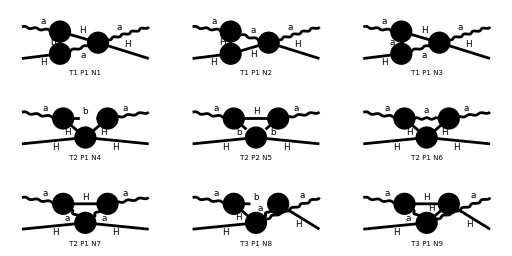

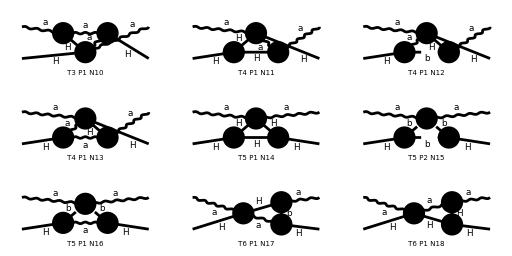

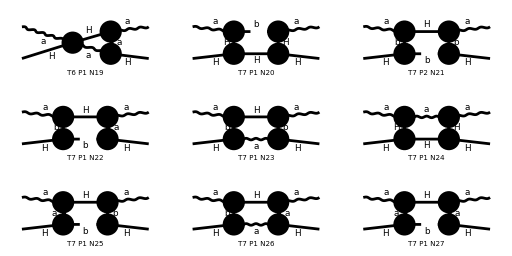

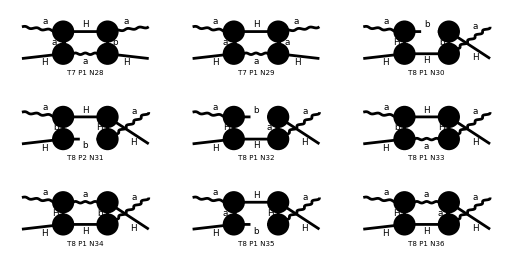

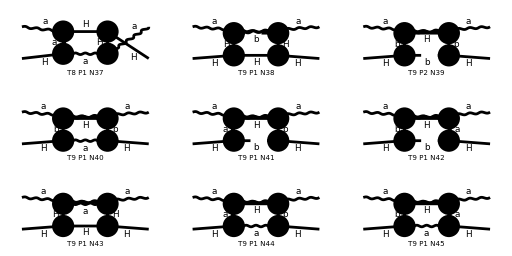

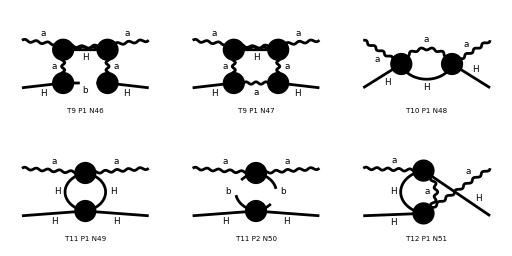

> Top. 1 aebe/cede/0.m, 0 diagrams

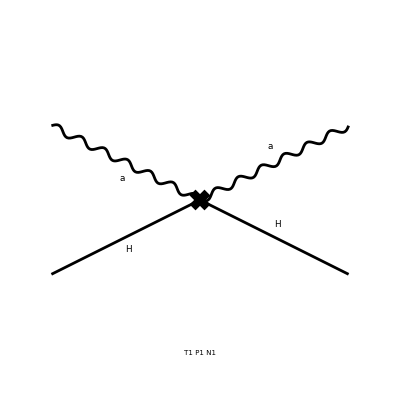

```mathematica
D1LAHAH=diag[1,{V[1],S[1]},{V[1],S[1]}];
```

```mathematica
Amp1LAHAH=D1LAHAH//amp1L[{p1,p1},{p1,p1}]
```

creating amplitudes at level(s) {Particles}

> Top. 1: 3 Particles amplitudes

> Top. 2: 4 Particles amplitudes

> Top. 3: 3 Particles amplitudes

> Top. 4: 3 Particles amplitudes

> Top. 5: 3 Particles amplitudes

> Top. 6: 3 Particles amplitudes

> Top. 7: 10 Particles amplitudes

> Top. 8: 8 Particles amplitudes

> Top. 9: 10 Particles amplitudes

> Top. 10: 1 Particles amplitude

> Top. 11: 2 Particles amplitudes

> Top. 12: 1 Particles amplitude

in total: 51 Particles amplitudes

creating amplitudes at level(s) {Particles}

> Top. 1: 1 Particles amplitude

in total: 1 Particles amplitude

{(ⅈ vev^4 g^Lor1Lor3 g^Lor2Lor6 g^Lor4Lor8 g^Lor5Lor7 (-((1-ξ_(V(1)))^3 (l-p1)^Lor3 (p1-l)^Lor4 (l-p1)^Lor5 (p1-l)^Lor6 l^Lor7 l^Lor8)/1+6+1-1/1+(g^Lor3Lor4 g^Lor5Lor6 g^Lor7Lor8)/((l^2-(g4 vev^2)/2).((l-p1)^2-e^2 vev^2).(l^2-e^2 vev^2).((l-p1)^2-e^2 vev^2))) e^8)/π^4+(ⅈ vev^4 g^Lor1Lor3 1 1 g^11 (11+1/1) e^8)/π^4+(3 7 e^6)/(4 π^4)+45+1/1+(ⅈ 4 (e 1+e 1))/(16 π^4)+(ⅈ (e (1)^Lor1-e 1) 111 (1) (g^Lor3Lor4/((l^2-e^2 vev^2 ξ_(V(1))).(1).1.((1)^2-(g4 1)/2))+((1-ξ_1) 1 1^Lor4)/1))/(16 π^4),1}
 |  |  |  |

```mathematica
Amp1LAHAHDiv=Amp1LAHAH//amp1LSimplify[{ZAAHH:> 1+Nd dAAHH,ZH:> 1+Nd dH,ZA:> 1+Nd dA},{SMP["Delta"],dAAHH,dH,dA},True]
```

Current diagram:       Number of diagrams: 51

Time: 390.682 s

2 dA e^2 g^Lor1Lor2+2 dAAHH e^2 g^Lor1Lor2+2 dH e^2 g^Lor1Lor2-(3 Δ e^4 g^Lor1Lor2)/(4 π^2)+(Δ e^4 ξ_(V(1)) g^Lor1Lor2)/(4 π^2)

```mathematica
dsol[18]=Solve[SelectNotFree2[Amp1LAHAHDiv/.dSub[dAAHH],{SMP["Delta"],dAAHH}]==0,dAAHH]//Flatten//Simplify
dSave[dsol[18]];
```

{dAAHH→(Δ e^2)/(24 π^2)}

## Final answers

```mathematica
dvalues
```

{dv→(Δ (3 (8 e^4+g4^2)+2 e^2 g4 ξ_(V(1))))/(32 π^2 g4),dH→-(Δ e^2 (ξ_(V(1))-3))/(8 π^2),dmH→(Δ (g4-3 e^2))/(16 π^2),dA→-(Δ e^2)/(24 π^2),dmA→-(Δ (72 e^4-20 e^2 g4+9 g4^2))/(96 π^2 g4),db→-(Δ e^2 (ξ_(V(1))-3))/(8 π^2),dmb→-(3 Δ (8 e^4+2 e^2 g4+g4^2))/(32 π^2 g4),dc→0,dmc→(Δ e^2 ξ_(V(1)))/(16 π^2),dHHH→(Δ (24 e^4-18 e^2 g4+7 g4^2))/(32 π^2 g4),dAAH→-(Δ (72 e^4-22 e^2 g4+9 g4^2))/(96 π^2 g4),dbbH→(Δ (24 e^4-18 e^2 g4+7 g4^2))/(32 π^2 g4),dAbH→(Δ e^2)/(48 π^2),dccH→-(3 Δ (8 e^4+2 e^2 g4+g4^2))/(32 π^2 g4),dHHHH→(Δ (24 e^4-12 e^2 g4+5 g4^2))/(16 π^2 g4),dbbHH→(Δ (24 e^4-12 e^2 g4+5 g4^2))/(16 π^2 g4),dAAbb→(Δ e^2)/(24 π^2),dAAHH→(Δ e^2)/(24 π^2)}

```mathematica
M$IntParams
```

{mA→e vev,mb→e vev √xiSubscript[V(1)],mc→e vev √xiSubscript[V(1)],mH→(√g4 vev)/(√2)}